## Expressions

We have dealt quite a bit with expressions

e.g.

```mathematica
x
```

x

```mathematica
x+x
```

2 x

```mathematica
a*x^2+b*x+c
```

c+b x+a x^2

Lists...

```mathematica
{x,0,1}
```

{x,0,1}

Plots...

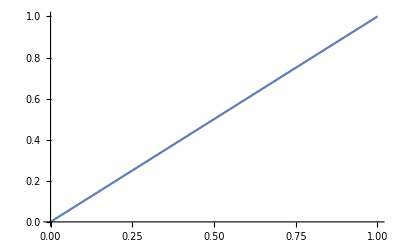

```mathematica
Plot[x,{x,0,1}]
```

Equations...

```mathematica
a*x^2+b*x+c==0
```

c+b x+a x^2==0

Functions

```mathematica
addOne[x_]:=x+1
```

Rules

```mathematica
n->10
```

n→10

## More complicated expressions

Let’s return to our quadratic equation

```mathematica
quadratic=a*x^2+b*x+c
```

c+b x+a x^2

We can decompose it into atoms:

```mathematica
FullForm[quadratic]
```

Plus[c,Times[b,x],Times[a,Power[x,2]]]

We see that this expression is created using nested symbols and numbers

The nested structure can be visualized intuitively using TreeForm

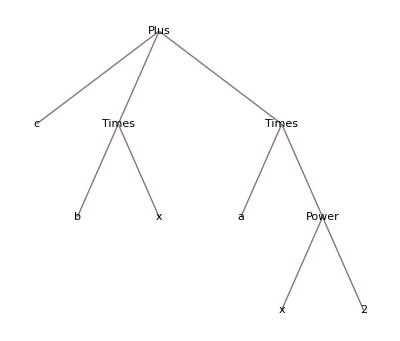

```mathematica
TreeForm[quadratic]
```

## Extracting parts of expressions

We can programmatically extract parts of expressions:

Recall:

```mathematica
quadratic//TreeForm
```

-Graphics-

The root of the expression tree can be obtained by calling Head

```mathematica
Head[quadratic]
```

Plus

This is always the same thing as getting the 0th index:

```mathematica
quadratic⟦0⟧
```

Plus

The “levels” of this tree can be extracted using Level

```mathematica
Level[quadratic,{0}]
```

{c+b x+a x^2}

```mathematica
Level[quadratic,{1}]
```

{c,b x,a x^2}

```mathematica
Level[quadratic,{2}]
```

{b,x,a,x^2}

```mathematica
Level[quadratic,{3}]
```

{x,2}

```mathematica
Level[quadratic,{4}]
```

{}

## More sophisticated expressions

```mathematica
plt=Plot[x,{x,0,1}]
```

-Graphics-

```mathematica
FullForm[plt]
```

Graphics[List[List[List[List[],List[],List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[2.04082×10^-8,2.04082×10^-8],List[0.000306718,0.000306718],List[0.000613415,0.000613415],List[0.00122681,0.00122681],List[0.0024536,0.0024536],List[0.00490718,0.00490718],List[0.00981434,0.00981434],List[0.0196287,0.0196287],List[0.0409084,0.0409084],List[0.0607779,0.0607779],List[0.0802576,0.0802576],List[0.101388,0.101388],List[0.121109,0.121109],List[0.142481,0.142481],List[0.163463,0.163463],List[0.183035,0.183035],List[0.204257,0.204257],List[0.22407,0.22407],List[0.243493,0.243493],List[0.264567,0.264567],List[0.284231,0.284231],List[0.305546,0.305546],List[0.326471,0.326471],List[0.345986,0.345986],List[0.367151,0.367151],List[0.386907,0.386907],List[0.408314,0.408314],List[0.429331,0.429331],List[0.448938,0.448938],List[0.470196,0.470196],List[0.490044,0.490044],List[0.509502,0.509502],List[0.530611,0.530611],List[0.55031,0.55031],List[0.57166,0.57166],List[0.59262,0.59262],List[0.61217,0.61217],List[0.633371,0.633371],List[0.653162,0.653162],List[0.672563,0.672563],List[0.693616,0.693616],List[0.713258,0.713258],List[0.734551,0.734551],List[0.754434,0.754434],List[0.773927,0.773927],List[0.795071,0.795071],List[0.814805,0.814805],List[0.83619,0.83619],List[0.857186,0.857186],List[0.876771,0.876771],List[0.898007,0.898007],List[0.917833,0.917833],List[0.93727,0.93727],List[0.958357,0.958357],List[0.978034,0.978034],List[0.978378,0.978378],List[0.978721,0.978721],List[0.979407,0.979407],List[0.98078,0.98078],List[0.983526,0.983526],List[0.989017,0.989017],List[0.98936,0.98936],List[0.989704,0.989704],List[0.99039,0.99039],List[0.991763,0.991763],List[0.994509,0.994509],List[0.994852,0.994852],List[0.995195,0.995195],List[0.995881,0.995881],List[0.997254,0.997254],List[0.997597,0.997597],List[0.997941,0.997941],List[0.998627,0.998627],List[0.99897,0.99897],List[0.999314,0.999314],List[0.999657,0.999657],List[1.,1.]]]]]],List[],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Part[List[List[Identity,Identity],List[Identity,Identity]],1,2][Slot[1]]][Part[Slot[1],1]],Function[Part[List[List[Identity,Identity],List[Identity,Identity]],2,2][Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Part[List[List[Identity,Identity],List[Identity,Identity]],1,2][Slot[1]]][Part[Slot[1],1]],Function[Part[List[List[Identity,Identity],List[Identity,Identity]],2,2][Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,1],List[0.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

## Holding expressions

Consider the expression

```mathematica
expr=x+x
```

2 x

```mathematica
FullForm[expr]
```

Times[2,x]

Mathematica evaluates our input expression and converts it to a canonical form

If we want to maintain the original expression in unevaluated form, use Hold

```mathematica
uneval=Hold[x+x]
```

Hold[x+x]

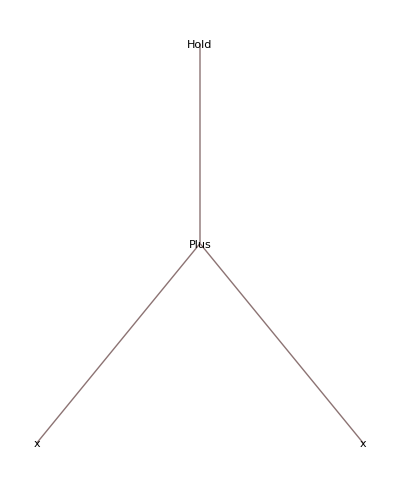

```mathematica
TreeForm[uneval]
```

Hold can be released using ReleaseHold

```mathematica
ReleaseHold[uneval]
```

2 x